```mathematica
(* we will do everything in terms of h-bar to make our life easier *)
hbar = 1;
P= 2;
psiX[x_] := (1/x)*Sqrt[2*hbar/(Pi*P)]*Sin[P*x/(2*hbar)];
probX[x_] := psiX[x]*Conjugate[psiX[x]];
psiP[p_] := Piecewise[{{0,p<-P/2},{1/Sqrt[P],-P/2<p<P/2},{0,p>P/2}}];
probP[p_] := psiP[x]*Conjugate[psiP[x]];
```

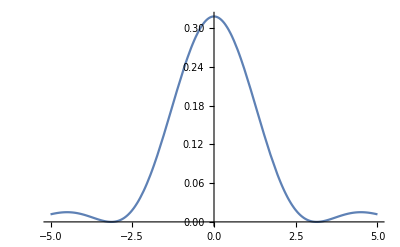

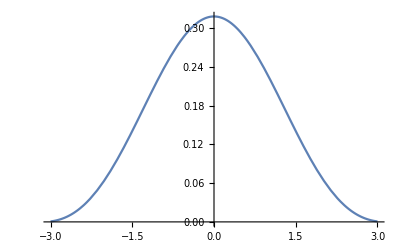

```mathematica
Plot[probX[x],{x,-5,5},PlotRange->All]
Plot[probX[x],{x,-3,3}]
```

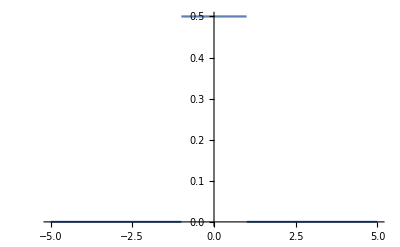

```mathematica
Plot[probP[x],{x,-5,5},PlotRange->All]
```

```mathematica
(* we can see from Out[9] that the first 0s will be at ±3hbar therefore we can guess that ∆x is about 3hbar. This is reasonable to do because this big curve is the majority of the probability so the particle will be found to have some x-value between the first 0s and thus the uncertainty in x is the width up to the 0s. This aligns with Heisenberg since the principle states the uncertainties have to be greater than or equal to hbar/2 and we can see with the plots above that ∆x = 3*hbar and ∆p = hbar and so we do not violate the principle.*)
```

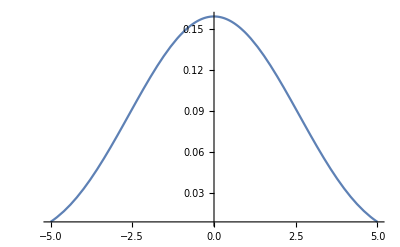

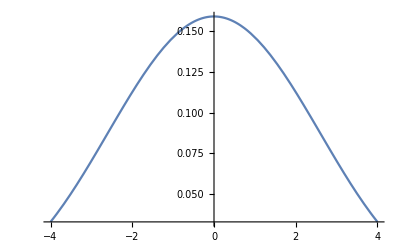

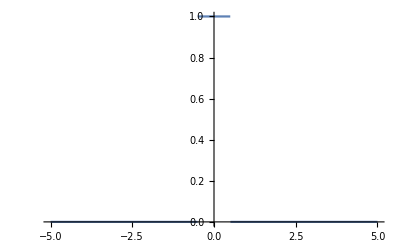

```mathematica
P= 1;
psiX[x_] := (1/x)*Sqrt[2*hbar/(Pi*P)]*Sin[P*x/(2*hbar)];
probX[x_] := psiX[x]*Conjugate[psiX[x]];
psiP[p_] := Piecewise[{{0,p<-P/2},{1/Sqrt[P],-P/2<p<P/2},{0,p>P/2}}];
probP[p_] := psiP[x]*Conjugate[psiP[x]];
Plot[probX[x],{x,-5,5},PlotRange->All]
Plot[probX[x],{x,-4,4}]
Plot[probP[x],{x,-5,5},PlotRange->All]
```

```mathematica
(* we can see as we decrease P, we increase ∆x (seen in Out[35] and Out[36]) and therefore decrease ∆p (seen in Out[37]. This behavior is expected due to Heisenberg's uncertainty principle *)
```